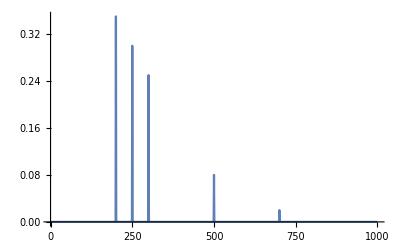

```mathematica
data={200,250,300,500,700};
A=EmpiricalDistribution[{35,30, 25,8,2}->data];
DiscretePlot[PDF[A,x],{x,0,1000},Joined->True]
```

```mathematica
vec=RandomVariate[A,100]
```

{250,300,250,250,300,200,250,200,300,200,300,200,250,200,500,200,200,250,300,200,300,250,700,300,200,250,250,300,300,250,700,200,500,250,200,250,500,250,500,300,300,250,500,250,250,300,250,300,250,300,200,250,300,200,200,200,250,250,250,500,250,250,300,200,250,200,200,200,250,250,200,200,200,200,250,300,300,250,250,300,250,300,200,500,300,300,250,250,250,200,200,250,200,250,300,200,500,200,200,250}

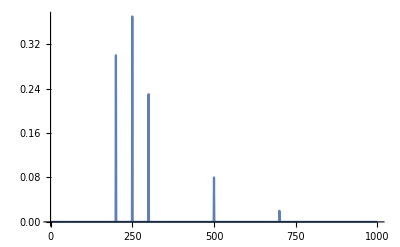

```mathematica
DiscretePlot[PDF[EmpiricalDistribution[vec],x],{x,0,1000},Joined->True]
```